## The SIR Model for Spread of Disease F. I. Giasemis

### Arnoud Buzing, Wolfram Research https://community.wolfram.com/groups/-/m/t/1903289

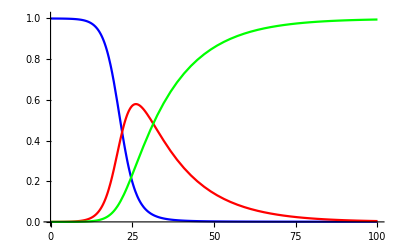

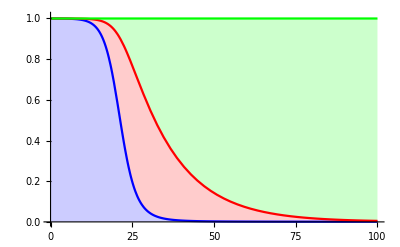

```mathematica
equationS=s'[t]==-b s[t] i[t];
equationI=i'[t]==b s[t]i[t]-k i[t];
equationR=r'[t]==k i[t];
b=.5;
k=1/14;
solution=NDSolve[{equationS,equationI,equationR,s[0]==0.9999,i[0]==0.0001,r[0]==0.0000},{s,r,i},{t,100}];
solutionS=First[s/.solution];
solutionI=First[i/.solution];
solutionR=First[r/.solution];
Plot[{solutionS[t],solutionI[t],solutionR[t]},{t,0,100},PlotRange->{0,1.01},PlotStyle->{Blue,Red,Green}]
Plot[{solutionS[t],solutionS[t]+solutionI[t],solutionS[t]+solutionI[t]+solutionR[t]},{t,0,100},PlotRange->{0,1.01},Filling->{1->Axis,2->{1},3->{2}},PlotStyle->{Blue,Red,Green}]
```

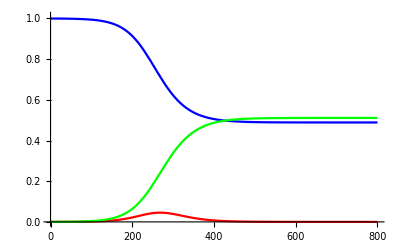

```mathematica
equationS=s'[t]==-b s[t] i[t];
equationI=i'[t]==b s[t]i[t]-k i[t];
equationR=r'[t]==k i[t];
b=.1;
k=1/14;
solution=NDSolve[{equationS,equationI,equationR,s[0]==0.9999,i[0]==0.0001,r[0]==0.0000},{s,r,i},{t,800}];
solutionS=First[s/.solution];
solutionI=First[i/.solution];
solutionR=First[r/.solution];
Plot[{solutionS[t],solutionI[t],solutionR[t]},{t,0,800},PlotRange->{0,1.01},PlotStyle->{Blue,Red,Green}]
```